```mathematica
PRÀCTICA 3: EQUACIONS,INEQUACIONS I EXTREMS RELATIUS DE FUNCIONS
```

```mathematica
f[x_]=(x^3-5x^2+3x+1)/(2x^2+x-1)
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x_]=Log[(x^2-1)/(2x-3)]
```

Log[(-1+x^2)/(-3+2 x)]

```mathematica
h[x_]=Sin[x/3]-Cos[x^3/5]
```

-Cos[x^3/5]+Sin[x/3]

```mathematica
ACTIVITAT 1
```

```mathematica
Solve[f[x]==0,x]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
N[%]
```

{{x→1.},{x→-0.236068},{x→4.23607}}

```mathematica
Per tant, les tres arrels de $f$ són: 2-√5, 1    i    2+√5
```

```mathematica
ACTIVITAT 2
```

```mathematica
Reduce[f[x]>0,x]
```

-1<x<2-√5||1/2<x<1||x>2+√5

```mathematica
Per tant, f(x) és positiva dins de la següent unió d'intervals: ]-1,2-√5[ U ]1/2,1[ U ]2+√5,+∞[
```

```mathematica
ACTIVITAT 3
```

```mathematica
Calculem primer la funció derivada de f(x):
```

```mathematica
u[x_]=D[f[x],x]
```

(3-10 x+3 x^2)/(-1+x+2 x^2)-((1+4 x) (1+3 x-5 x^2+x^3))/((-1+x+2 x^2)^2)

```mathematica
Ara resolem la inequació u(x)>0 :
```

```mathematica
Reduce[u[x]>0,x]
```

x<Root[1-#1+3 #1^2+#1^3&,1]||x>2

```mathematica
L'output indica que Reduce ens dóna la solució en funció d'una arrel d'un polinomi que no calcula exactament (x^3+3x^2-x+1). Però aplicant la instrucció N[] ens pot donar una aproximació d'aquesta arrel:
```

```mathematica
N[%]
```

x<-3.38298||x>2.

```mathematica
Per tant, f(x) és creixent en ]-∞, -3.38298[ U ]2,+∞[
```

```mathematica
ACTIVITAT 4
```

```mathematica
Calculem el domini de f:
```

```mathematica
Solve[2x-3==0,x]
```

{{x→3/2}}

```mathematica
El valor 3/2 no pertany al domini de g perquè anul.la al denominador de la funció racional a la qual afecta el logaritme.
```

```mathematica
Per altra banda, la funció logaritme només està definida per a nombres reals estrictament positius. Per tant, hem de resoldre la inequació: (x^2-1)/(2x-3)>0
```

```mathematica
Reduce [(x^2-1)/(2x-3)>0,x]
```

-1<x<1||x>3/2

```mathematica
Cal observar que Reduce ja exclou automàticament el valor 3/2 per anul.lar al denominador. El domini és, per tant:  D=]-1,1[ U ]3/2,+∞[
```

```mathematica
Calculem les asímptotes verticals. La primera candidata serà x=3/2, per anul.lar al denominador de la fracció algebraica que hi ha dins del logaritme. Veiem-ho:
```

```mathematica
Limit[g[x],x->3/2]
```

∞

```mathematica
Per tant, x=3/2 és una asímptota vertical. Com que la funció log(x) té a x=0 com a asímptota vertical, també seran candidates a asímptotes verticals de g aquells valors que anul.len a la fracció algebraica que hi ha dins del logaritme. Per tant, calculem...
```

```mathematica
Solve[x^2-1==0,x]
```

{{x→-1},{x→1}}

```mathematica
Limit[g[x],x->-1]
```

-∞

```mathematica
Limit[g[x],x->1]
```

-∞

```mathematica
Concloem que x=-1 i x=1 també són asímptotes verticals.
```

```mathematica
Calculem els extrems relatius:
```

```mathematica
Solve[g'[x]==0,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
Veiem que hi ha dos valors crítics. Una manera de saber si hi ha extrem relatiu és avaluant la segona derivada i substituint:
```

```mathematica
g''[x]/.x->1/2 (3-√5)
```

(√5 (3-√5) (-(3-√5)/(√5)-2/5 (-1+1/4 (3-√5)^2)))/((-1+1/4 (3-√5)^2)^2)+(2 (-(3-√5)/(√5)-2/5 (-1+1/4 (3-√5)^2)))/(-1+1/4 (3-√5)^2)-(√5 (-2/(√5)-4/5 (3-√5)-(8 (-1+1/4 (3-√5)^2))/(5 √5)))/(-1+1/4 (3-√5)^2)

```mathematica
N[%]
```

-2.34164

```mathematica
g''[x]/.x->1/2 (3+√5)
```

-(√5 (3+√5) ((3+√5)/(√5)-2/5 (-1+1/4 (3+√5)^2)))/((-1+1/4 (3+√5)^2)^2)+(2 ((3+√5)/(√5)-2/5 (-1+1/4 (3+√5)^2)))/(-1+1/4 (3+√5)^2)+(√5 (2/(√5)-4/5 (3+√5)+(8 (-1+1/4 (3+√5)^2))/(5 √5)))/(-1+1/4 (3+√5)^2)

```mathematica
N[%]
```

0.341641

```mathematica
Per tant, en el punt d'abcissa 1/2 (3-√5) hi ha un màxim relatiu, i en punt d'abcissa 1/2 (3+√5) hi ha un mínim relatiu. Calculem les ordenades dels dos punts.
```

```mathematica
g[1/2 (3-√5)]
```

Log[-(-1+1/4 (3-√5)^2)/(√5)]

```mathematica
Simplifiquem perquè no es veu clara la correspondència amb la solució del qüestionari:
```

```mathematica
Simplify[%]
```

Log[1/2 (3-√5)]

```mathematica
Per tant, M=(1/2 (3-√5), Log[1/2 (3-√5)])
```

```mathematica
g[1/2 (3+√5)]
```

Log[(-1+1/4 (3+√5)^2)/(√5)]

```mathematica
Simplify[%]
```

Log[1/2 (3+√5)]

```mathematica
Per tant:   m=(1/2 (3+√5), Log[1/2 (3+√5)])
```

```mathematica
ACTIVITAT 5
```

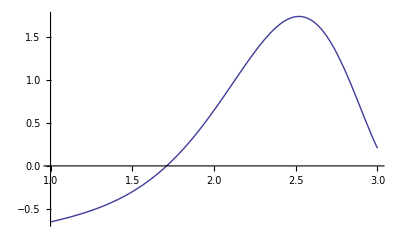

```mathematica
Plot[h[x],{x,1,3}]
```

```mathematica
Veiem que h(x) té un màxim relatiu a l'interval [1,3], que ha de ser necessàriament arrel de la primera derivada de h(x)
```

```mathematica
Solve[h'[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

```mathematica
No podem calcular els valors crítics de h(x) utilitzant Solve. Provem amb NSolve:
```

```mathematica
NSolve[h'[x]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

```mathematica
Tampoc podem. Tractarem ara de calcular l'arrel de h'(x) a l'interval [1,3] utilitzant FindRoot. Com a valor inicial, podem agafar x_0=2.5, que està molt proper al valor que busquem:
```

```mathematica
FindRoot[h'[x],{x,2.5}]
```

{x→2.51985}

```mathematica
Aquesta és una aproximació a l'abcissa del màxim relatiu. Però la volem amb 9 decimals exactes (és a dir, amb 10 xifres significatives exactes, en total). Per tant afegirem l'opció WorkingPrecision->10 a FindRoot:
```

```mathematica
FindRoot[h'[x],{x,2.5}, WorkingPrecision->10]
```

{x→2.519849493}

```mathematica
El valor demanat es 2.519849493
```